```mathematica
Remove["Global`*"];
```

```mathematica
fp={{0.50006,-12019.47},{0.5511,-8352.63},{0.59989,-5963.33},{0.64981,-4354.21},{0.69972,-3125.42},{0.75189,-2296.48},{0.79955,-1516.3},{0.85173,-1106.71},{0.90051,-687.36},{0.95269,-511.82},{0.99944,-4.7},{1.05026,131.83},{1.10017,229.35},{1.15009,365.88},{1.20226,453.65},{1.25015,726.71},{1.30096,912.01},{1.34998,1233.83},{1.39989,1506.89},{1.44868,1740.95},{1.50085,1965.25}}
```

{{0.50006,-12019.5},{0.5511,-8352.63},{0.59989,-5963.33},{0.64981,-4354.21},{0.69972,-3125.42},{0.75189,-2296.48},{0.79955,-1516.3},{0.85173,-1106.71},{0.90051,-687.36},{0.95269,-511.82},{0.99944,-4.7},{1.05026,131.83},{1.10017,229.35},{1.15009,365.88},{1.20226,453.65},{1.25015,726.71},{1.30096,912.01},{1.34998,1233.83},{1.39989,1506.89},{1.44868,1740.95},{1.50085,1965.25}}

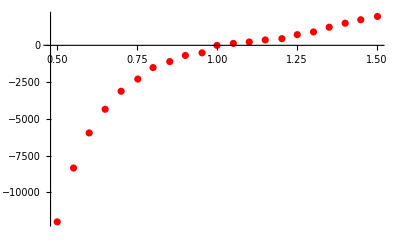

```mathematica
gp=ListPlot[fp,PlotStyle->Red]
```

```mathematica
K=148000;
```

```mathematica
fun=2/(3 Subscript[λ, 1])(Subscript[u, 1](Subscript[λ, 1]^(2/3(1-Subscript[b, 1])Subscript[α, 1])-Subscript[λ, 1]^(1/3(Subscript[b, 1]-1)Subscript[α, 1]))+Subscript[u, 2](Subscript[λ, 1]^(2/3(1-Subscript[b, 1])Subscript[α, 2])-Subscript[λ, 1]^(1/3(Subscript[b, 1]-1)Subscript[α, 2])))+1/2 K (Subscript[λ, 1]^(1+4 Subscript[b, 1])-Subscript[λ, 1]^-1);
```

{u_1→-122.769,u_2→-96.6491,α_1→-5.06279,α_2→0.232932,b_1→-0.482849}

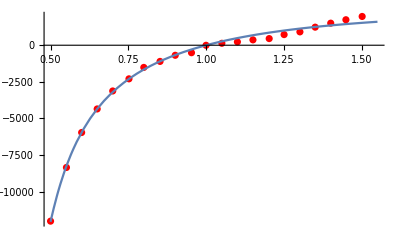

```mathematica
fit=FindFit[fp,{fun,{-∞<=Subscript[u, 1]≤∞,-∞<=Subscript[u, 2]≤∞,-∞<=Subscript[α, 1]≤∞,-∞<=Subscript[α, 2]≤∞,-0.6<=Subscript[b, 1]≤-0.4}},{Subscript[u, 1],Subscript[u, 2],Subscript[α, 1],Subscript[α, 2],Subscript[b, 1]},Subscript[λ, 1],Method->NMinimize]
Show[gp,Plot[fun/.fit,{Subscript[λ, 1],0.5,1.55}],PlotRange-> All]
```

```mathematica
fun1=1/x^Subscript[b, 2](1/3(Subscript[u, 1](x^(1/3(Subscript[b, 2]-1)Subscript[α, 1])-x^(2/3(1-Subscript[b, 2])Subscript[α, 1]))+Subscript[u, 2](x^(1/3(Subscript[b, 2]-1)Subscript[α, 2])-x^(2/3(1-Subscript[b, 2])Subscript[α, 2])))+1/2 K (x^(2+4 Subscript[b, 2])-1))/.{Subscript[u, 1]->-122.76934572390621,Subscript[u, 2]->-96.64913804244887,Subscript[α, 1]->-5.06279239138198,Subscript[α, 2]->0.23293206532810481,Subscript[b, 1]->-0.4828491481371017};
```

```mathematica
%20
```

x^-b_2 (1/2 K (-1+x^(2+4 b_2))+1/3 (-122.769 (-x^(-3.37519 (1-b_2))+x^(-1.6876 (-1+b_2)))-96.6491 (-x^(0.155288 (1-b_2))+x^(0.077644 (-1+b_2)))))

```mathematica
Solve[{fun1==0},{x}];
```

Solve::inex: Solve 无法求解具有不精确系数的系统，或是通过将系统中出现的不精确数直接合理化处理得到的系统. 由于 Solve 所用的许多方法需要精确输入，为 Solve 提供一个精确版本的系统可能会有帮助.